```mathematica
(* Defines SU(2) *)
Jz[j_] :=DiagonalMatrix[ Table[m,{m,j,-j,-1}]] 
Jp[j_] :=DiagonalMatrix[ Table[Sqrt[(j-m)(j+m+1)],{m,j-1,-j,-1}],1]
Jm[j_] :=DiagonalMatrix[ Table[Sqrt[(j-m)(j+m+1)],{m,j-1,-j,-1}],-1]
```

```mathematica
(* Setup *)
j=3;
ω=1;
g=0.5;
```

```mathematica
(* Numeric solution *)
H =N[ω Jz[j] +g (Jp[j] + Jm[j])];
ψini = Partition[Table[KroneckerDelta[-j,m],{m,-j,j,1}],1];
```

```mathematica
(* Graph eigenvalues *)
(*{eval,evec}=Eigensystem[H];
Plot[{Re[eval/.ω->1],Im[eval/.ω->1]},{g,0,2}]*)
```

```mathematica
(* Analytic solution *)
Jy[j_]:=(Jp[j] - Jm[j])/(2ⅈ);
β [ω_,g_]:= ArcTan[2g/ω];
Ua[j_,ω_,g_,z_]:= MatrixExp[-ⅈ Jy [j]β[ω,g]]. MatrixExp[ⅈ Sqrt[ω^2 + 4 g^2] Jz[j]z].MatrixExp[ⅈ Jy [j]β[ω,g]]
```

```mathematica
(* Defines the differential equation and initial condition *)
deq={ -ⅈ Ψ'[z] == H.Ψ[z] };
ini ={ Ψ[0]==ψini};

rule=Flatten[ NDSolve[Flatten[{deq,ini}],Ψ[z],{z,0,100}]]
```

{Ψ[z]→InterpolatingFunction[{{0., 100.}}, <>][z]}

```mathematica
zmax = 18;
```

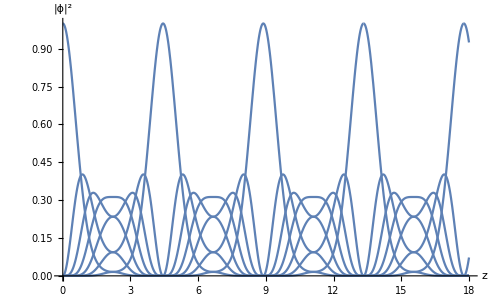

```mathematica
Plot[ Abs[ Ψ[z]/.rule ]^2,{z,0,zmax},
PlotRange->{{0,zmax},{0,1}},
AxesLabel->{"z","|ϕ|^2"}]
```

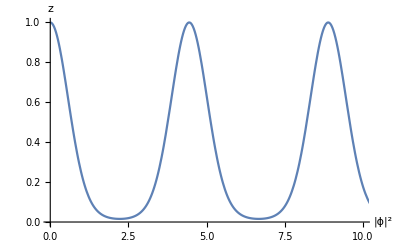
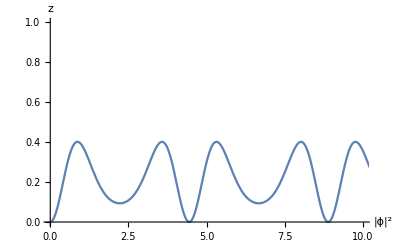
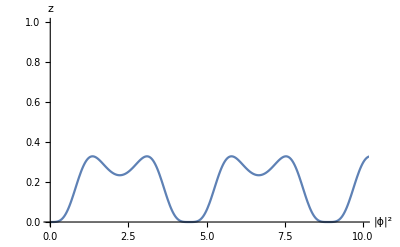
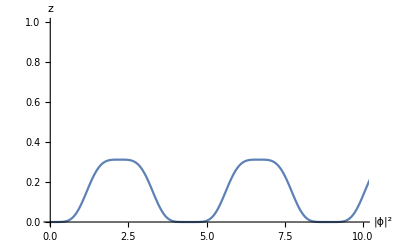
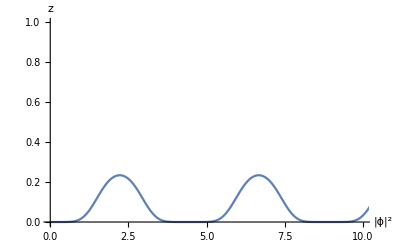
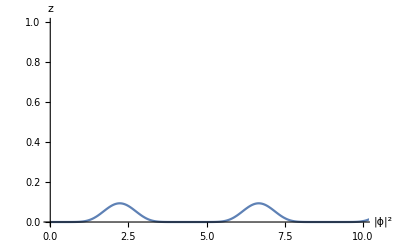
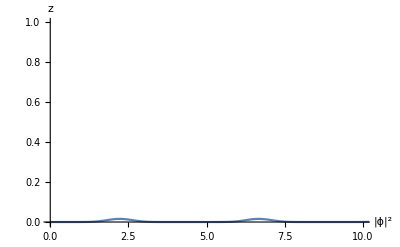

```mathematica
Table[Plot[ (Abs[ Ψ[z]/.rule ]^2)[[j]],{z,0,100},
PlotRange->{{0,10},{0,1}},
AxesLabel->{"|ϕ|^2","z"}],{j,1,2j+1}]
```

```mathematica
(* Calculates the analytic solution *)
ϕ=Ua[j,ω,g,z].ψini ;
```

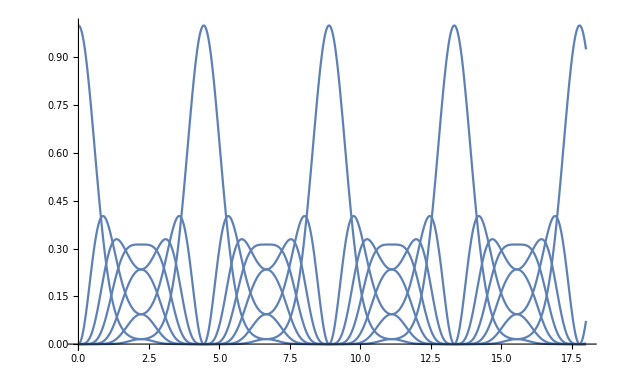

```mathematica
Plot[ Abs[ϕ]^2,{z,0,zmax},PlotRange->{{0,zmax},{0,1}}]
```

```mathematica
(* Errror *)
```

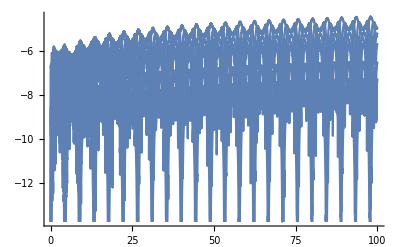

```mathematica
Plot[Log[10,Abs[ Abs[ Ψ[z]/.rule ]^2 - Abs[ϕ]^2]] ,{z,0,100}]
```